```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
e=1;
m=6;
P=2^m;
Ep=4;
W$=Table[0,{i,1,Ep}];
WMG=Table[0,{i,1,Ep}];
WBG=Table[0,{i,1,Ep}];
Dynamic[{Ep,e,t}]
SetSharedVariable[e,W$,WMG,WBG]
```

```mathematica
ParallelEvaluate[(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=100-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,1},{j,1,3}]~Join~Table[0,{i,1,n-1},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[100,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
BS⟦1,3⟧=BS⟦1,2⟧;
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];Do[W⟦i⟧=100,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦1,s⟧=0,{s,1,S}];,
Do[PayoffFunction⟦1,s⟧=(AgentStrategy⟦1,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";If[t>T,Goto[sample],Goto[begin]];
Label[sample];
W$⟦e⟧=W⟦1⟧;
WMG⟦e⟧=W⟦2⟧;
WBG⟦e⟧=Mean[W⟦3;;n⟧];
e=e+1;
If[e>Ep,Break,Goto[New]];),(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=100-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,1},{j,1,3}]~Join~Table[0,{i,1,n-1},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[100,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
BS⟦1,3⟧=BS⟦1,2⟧;
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];Do[W⟦i⟧=100,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦1,s⟧=0,{s,1,S}];,
Do[PayoffFunction⟦1,s⟧=(AgentStrategy⟦1,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";If[t>T,Goto[sample],Goto[begin]];
Label[sample];
W$⟦e⟧=W⟦1⟧;
WMG⟦e⟧=W⟦2⟧;
WBG⟦e⟧=Mean[W⟦3;;n⟧];
e=e+1;
If[e>Ep,Break,Goto[New]];)]//AbsoluteTiming
```

{3.11618,ParallelEvaluate[Label[New];n1=1;$ player;n2=1;MG player;n3=99;Back ground;n=n1+n2+n3;T=100-1;odd steps needs;mu=Table[0,{i,1,T}];normalize=1/(√n);S=2;t=3;mu⟦1⟧=RandomInteger[P-1];mu⟦2⟧=RandomInteger[P-1];signal=0;bestStrategy⟦i⟧,U⟦i,s⟧;Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book;StategySpace-->we don't construck it;Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]];AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy;PayoffFunction=Table[0,{i,1,n},{s,1,S}];A=Table[0,{i,1,T}];bestStrategy=Table[0,{i,1,n},{j,1,2}];bestStrategy⟦Fresh,React⟧;BS=Join[Table[0,{i,1,1},{j,1,3}],Table[0,{i,1,n-1},{j,1,2}]];U=Table[1,{i,1,n},{i,1,S}];Price=Table[0,{i,1,T}];Price⟦2⟧=Price⟦1⟧=10;Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10;W=Table[100,{i,1,n}];c=Table[100,{i,1,n}];NStock=Table[0,{i,1,n},{i,1,2}];AgentStrategy=Table[0,{i,1,n},{i,1,S}];initial set;AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];Label[begin];Nature choice;mu⟦t⟧=RandomInteger[P-1];mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P];group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order;Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];BS⟦1,3⟧=BS⟦1,2⟧;Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];];Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t);MarketAction=0;Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];A⟦t⟧=MarketAction;signal=UnitStep[MarketAction];Price/Cash/Wealth update deal t+1 ;Price⟦t⟧=Price⟦t-1⟧+normalize A⟦t-1⟧;If[t==3,Do[c⟦i⟧=100,{i,1,n}];Do[NStock⟦i,2⟧=0,{i,1,n}];Do[W⟦i⟧=100,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧ Price⟦t⟧;c⟦i⟧=N[c⟦i⟧],{i,1,n}];Do[NStock⟦i,1⟧=NStock⟦i,2⟧;NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧ (Price⟦t⟧-Price⟦t-1⟧);W⟦i⟧=N[W⟦i⟧],{i,1,n}];];Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t);If[OddQ[t],Do[PayoffFunction⟦1,s⟧=0,{s,1,S}];,Do[PayoffFunction⟦1,s⟧=AgentStrategy⟦1,s⟧⟦mu⟦t-1⟧+1⟧ A⟦t⟧,{s,1,S}];] Do[PayoffFunction⟦i,s⟧=-AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧ A⟦t⟧,{s,1,S},{i,n1+1,n}];Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];t=t+1;Go on or Stop;If[t>T,Goto[sample],Goto[begin]];Label[sample];W$⟦e⟧=W⟦1⟧;WMG⟦e⟧=W⟦2⟧;WBG⟦e⟧=Mean[W⟦3;;n⟧];e=e+1;If[e>Ep,Break,Goto[New]];,Null]}

```mathematica
(246*250)/3600//N
```

17.0833

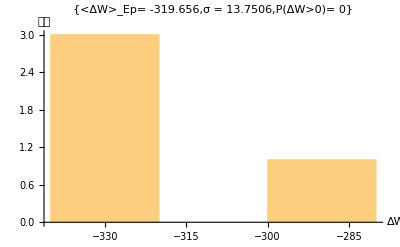

```mathematica
Histogram[W$-100,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[W$-100]]],"σ = "<>ToString[N[StandardDeviation[W$-100]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[W$-100]],3]]}]
```

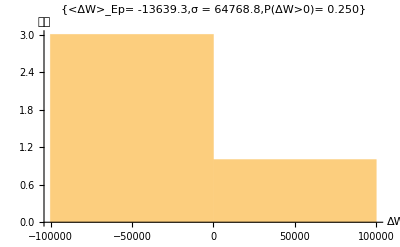

```mathematica
Histogram[WMG-100,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WMG-100]]],"σ = "<>ToString[N[StandardDeviation[WMG-100]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WMG-100]],3]]}]
```

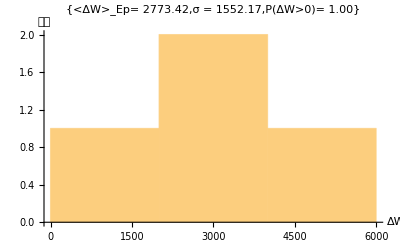

```mathematica
Histogram[WBG-100,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WBG-100]]],"σ = "<>ToString[N[StandardDeviation[WBG-100]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WBG-100]],3]]}]
```

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

```mathematica
N[Variance[A]]
```

55.9457

```mathematica
1/(n*T)Sum[(A⟦i⟧-(Mean[A]))^2,{i,1,T}]//N
```

0.553572

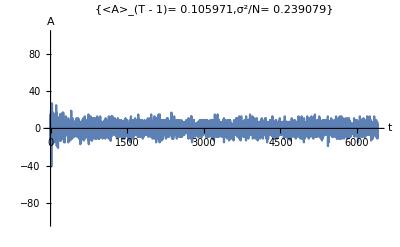

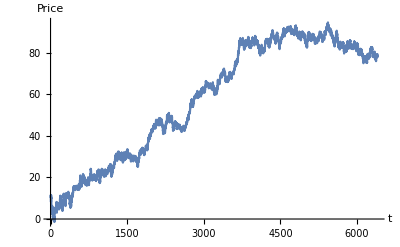

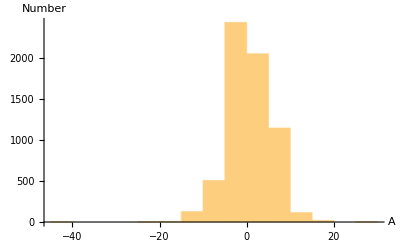

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->{"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]],"σ^2/N= "<>ToString[N[1/n Variance[A]]]}]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

```mathematica
1/(n*T)Sum[(A⟦i⟧)^2,{i,1,n}]//N
```

0.465607

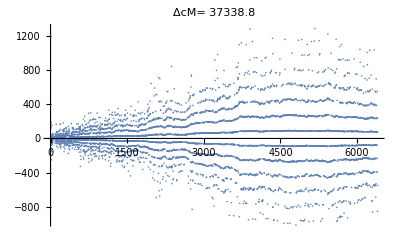

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦1;;T⟧]]]]
```

```mathematica
-Total[ΔcM⟦1;;T⟧]+(9n-nM⟦T⟧)*Price⟦T⟧-(9n*Price⟦1⟧)//N
```

```mathematica
W⟦1⟧
```

-197.516

```mathematica
W⟦2⟧
```

8532.94

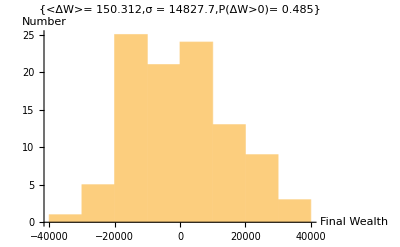

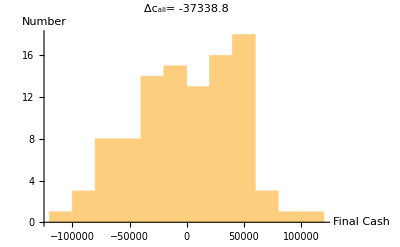

```mathematica
f4=Histogram[W⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Wealth","Number"},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-100]]],"σ = "<>ToString[N[StandardDeviation[W-100]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-100]],3]]}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
c
```

{-117.913,2742.89,-6467.88,507.166,-15793.9,-7877.01,2937.71,12886.8,16011.4,5602.37,-2623.22,13986.4,8147.35,-585.691,-15287.1,-10469.4,7017.31,11421.5,-3769.09,-1811.38,-15420.,-13.6204,-12353.,-4512.65,-15424.3,-1994.65,-12016.4,-13632.5,3716.09,10951.5,7743.28,7701.99,4525.05,4759.5,-12894.1,10824.7,-8774.24,13832.5,-12025.,22391.8,7784.61,7711.14,-1155.05,3723.66,-4565.58,5531.06,12931.2,12880.6,6209.06,-12902.7,-12179.5,65.8824,-8060.59,-6415.14,-11475.,14451.6,8774.72,-16664.1,1988.24,-7848.19,-7736.45,-5882.2,8294.03,702.29,4445.94,-12353.,-6144.4,-9079.44,-15455.4,11760.8,-7721.12,16191.8,-6664.5,-11517.2,-10866.5,22351.9,485.469,-6436.84,-6529.36,10912.,-6418.1,-3852.37,-11626.9,-5141.01,-1659.12,6960.28,4652.83,-9069.69,6844.47,14452.5,-16676.,-11381.2,-2028.88,-11958.1,507.166,-4742.42,-8723.7,-15356.6,-926.169,14451.6,14442.8}